## Function to Solve Equation

```mathematica
functionSolve[ldev_,l0_,ϕ_,γ_,δy_,yf_,yDe_,zDe_,yPDe_,zPDe_,tDe_]:=Module[{solutions,seeds,sol,fulsoly,fulsolz,dsoly,dsolz,sol2,times,ys,tf,tDeU,yDeU,zDeU,yPDeU,zPDeU,yfU,period,Δz,ΔzP,Δt,steplength,speedND,stepfreq,ke,dke,pe,dpe,totalsynctime,percentCong},
period=4Pi;
solutions={};
seeds=Table[i,{i,tDe+0.2,tDe+period,0.25}];
leq[t]=l0-ldev Cos[(t-tDe)];
ltri[t]=Sqrt[(y[t]-yf)^2+(z[t])^2];
fk[t]=(leq[t]-ltri[t]);

sol=NDSolve[{ y''[t]==ϕ^2(fk[t])(y[t]-yf)/(ltri[t]),
z''[t]==ϕ^2((fk[t])(z[t])/(ltri[t]))-γ
,y[tDe]==yDe,y'[tDe]==yPDe,z[tDe]==zDe,z'[tDe]==zPDe},{y[t],z[t]},{t,tDe,tDe+period}];

fulsoly=(y[t]/.sol)[[1]];
fulsolz=(z[t]/.sol)[[1]];
dsoly=D[fulsoly,t];
dsolz=D[fulsolz,t];

Do[
sol2=Quiet@FindRoot[dsoly==yPDe,{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
];

times=Select[t/.solutions,(tDe+0.2)<#<(tDe+period)&];
ys=Flatten[(dsoly/.t->times)];
tf=Table[(ys[[i]]-yPDe)<10^-6,{i,1,Length[ys]}];


tDeU=Min[DeleteDuplicates[Pick[times,tf]]];
yDeU=(fulsoly/.t->tDeU);
zDeU=(fulsolz/.t->tDeU);
yPDeU=(dsoly/.t->tDeU);
zPDeU=(dsolz/.t->tDeU);
yfU=yDeU+Abs[δy];

Δz=Abs[Abs[zDe]-Abs[zDeU]];
ΔzP=Abs[Abs[zPDe]-Abs[zPDeU]];

Δt=tDeU-tDe;
steplength=yDeU-yDe;
speedND=steplength/Δt;
stepfreq=1/Δt;



{{yfU,yDeU,zDeU,yPDeU,zPDeU,tDeU},{steplength,speedND,stepfreq},{Δz,ΔzP},{tDe,fulsoly,fulsolz,Δt,yf}}

]

tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.02}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.009},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]
```

## Influence of Ratio

```mathematica
ratio=Table[i,{i,1,4,0.1}]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
results=Table[Module[{ϕ=0.3,γ=0.01,init={0,-0.05,1,0.015,0,0},output,iteration=0,state,ldev=i*1,l0=1,δy=-0.05,ke,dke,pe,dpe,totalsynctime,percentCong,zmin,zmax,amp,energyC,grf,grfmin,grfmax},(*Initial state*)

output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@init];

While[Or@@Thread[Abs[output[[3]]]>=10^-4]&&iteration<=1000,
state=output[[1]];
output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@state];
iteration++;];

ke=(0.5*(Sqrt[D[output[[4,2]],t]^2+D[output[[4,3]],t]^2]));
dke=D[ke,t];
pe=(γ(output[[4,3]]));
dpe=D[pe,t];
syncCondition[t]=Piecewise[{{1,dpe*dke>0}},0];
totalsynctime=Quiet@Check[NIntegrate[syncCondition[t],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
percentCong=(totalsynctime/output[[4,4]])*100;

zmin=Quiet@Check[First[FindMinimum[{output[[4,3]],output[[4,1]]<t<output[[1,6]]},{t,(output[[1,6]]+output[[4,1]])/2}]],$Failed];
zmax=output[[4,3]]/.t->output[[4,1]];
amp=(zmax-zmin)/2;
energyC=Quiet@Check[NIntegrate[Abs[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2])(D[(l0-ldev Cos[t-output[[4,1]]]),t])],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
grfmax=Abs[First[Quiet[FindMaximum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[4,1]],output[[1,6]]}]]]];
grfmin=Abs[First[Quiet[FindMinimum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[1,6]],output[[4,1]]}]]]];
grf=Max[grfmin,grfmax];





{output,iteration,{percentCong,amp,energyC,grf}}

],{i,ratio}];
```

$Aborted

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\Ratio.mx",results];
```

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\Ratio.mx"];
```

```mathematica
resultsUU=Table[ReplacePart[results[[i]],1->Delete[results[[i,1]],4]],{i,1,Length[ratio]}];
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
trueresults=Pick[results,truefalse];
trueϕγ=Pick[ratio,truefalse];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
resultsU=filterPoints[resultsUU][[1]];
ϕγU=filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
grf=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
pointsSL=Transpose[{ϕγU,steplength}];
pointsV=Transpose[{ϕγU,speedND}];
pointsSF=Transpose[{ϕγU,stepFreq}];
pointsPC=Transpose[{ϕγU,perCong}];
pointsCon=Transpose[{ϕγU,convergP}];
pointsamp=Transpose[{ϕγU,amp}];
pointsengC=Transpose[{ϕγU,engC}];
pointsgrf=Transpose[{ϕγU,grf}];
```

```mathematica
Needs["MaTeX`"]
```

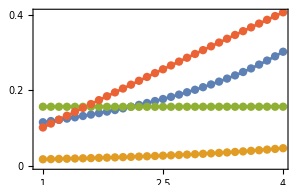

```mathematica
plot11=ListPlot[{pointsSL,pointsV,pointsSF,pointsamp},Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},(*PlotLegends->LineLegend[Automatic,{"Step Length, v","Speed","Step Frequency, 1/(Δτ)","Amp"}],*)FrameLabel->{{None,None},{MaTeX["\\LARGE \\text{$\\ell_\\text{d}$}"],None}},ImageSize->{300,200},MeshStyle->PointSize[0.02],FrameTicks->{{tiksfunc[{0,0.2,0.4}],Automatic},{tiksfunc[{1,2.5,4}],Automatic}}]
```

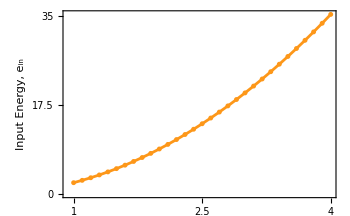

```mathematica
plot111=ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,18,FontFamily->"Latin Modern Roman 10"},PlotStyle->ColorData["SunsetColors",0.6],FrameStyle->{{ColorData["SunsetColors",0.6],None},{None,None}},ImageSize->{350,230},MeshStyle->PointSize[0.01],FrameLabel->{{"Input Energy, e_in",None},{MaTeX["\\LARGE \\text{$\\ell_\\text{d}$}"],None}},FrameTicks->{{tiksfunc[{0,17.5,35}],Automatic},{tiksfunc[{1,2.5,4}],Automatic}}]
(*plot112=ListPlot[pointsgrf,Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,18,FontFamily->"Latin Modern Roman 10"},ImageSize->{350,230},FrameStyle->{{RGBColor[0.2,0.5,0.6],None},{None,None}},PlotStyle->RGBColor[0.2,0.5,0.6],MeshStyle->PointSize[0.02]];
plot12=ResourceFunction["CombinePlots"][plot111,plot112,"AxesSides"->"TwoY",Frame->True,ImageSize->{350,230},FrameLabel->{{"Input Energy, e_in","Abs(GRF)_max"},{MaTeX["\\LARGE \\text{$\\ell_\\text{d}$}"],None}},ImagePadding->{{50,40},{60,10}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"}]*)
```

```mathematica
FindFit[pointsamp,a x +b,{a,b},x]
```

{a→0.101418,b→0.00196767}

```mathematica
FindFit[pointsamp,a x +b,{a,b},x]
```

{a→0.101418,b→0.00196767}

```mathematica
FindFit[Transpose[{grf,amp}],a x +b,{a,b},x]
```

{a→0.0910898,b→-0.00871606}

## Influence of initial forward speed

```mathematica
y0D=Table[i,{i,0.013,0.08,0.0025}]
```

{0.013,0.0155,0.018,0.0205,0.023,0.0255,0.028,0.0305,0.033,0.0355,0.038,0.0405,0.043,0.0455,0.048,0.0505,0.053,0.0555,0.058,0.0605,0.063,0.0655,0.068,0.0705,0.073,0.0755,0.078}

```mathematica
results=Table[Module[{ϕ=0.3,γ=0.01,init={0,-0.05,1,i,0,0},output,iteration=0,state,ldev=1.5*1,l0=1,δy=-0.05,ke,dke,pe,dpe,totalsynctime,percentCong,zmin,zmax,amp,energyC,grf,grfmin,grfmax},(*Initial state*)

output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@init];

While[Or@@Thread[Abs[output[[3]]]>=10^-4]&&iteration<=1000,
state=output[[1]];
output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@state];
iteration++;];

ke=(0.5*(Sqrt[D[output[[4,2]],t]^2+D[output[[4,3]],t]^2]));
dke=D[ke,t];
pe=(γ(output[[4,3]]));
dpe=D[pe,t];
syncCondition[t]=Piecewise[{{1,dpe*dke>0}},0];
totalsynctime=Quiet@Check[NIntegrate[syncCondition[t],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
percentCong=(totalsynctime/output[[4,4]])*100;

zmin=Quiet@Check[First[FindMinimum[{output[[4,3]],output[[4,1]]<t<output[[1,6]]},{t,(output[[1,6]]+output[[4,1]])/2}]],$Failed];
zmax=output[[4,3]]/.t->output[[4,1]];
amp=(zmax-zmin)/2;
energyC=Quiet@Check[NIntegrate[Abs[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2])(D[(l0-ldev Cos[t-output[[4,1]]]),t])],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
grfmax=Abs[First[Quiet[FindMaximum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[4,1]],output[[1,6]]}]]]];
grfmin=Abs[First[Quiet[FindMinimum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[1,6]],output[[4,1]]}]]]];
grf=Max[grfmin,grfmax];






{output,iteration,{percentCong,amp,energyC,grf}}

],{i,y0D}];
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\y0D.mx",results];
```

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\y0D.mx"];
```

```mathematica
resultsUU=Table[ReplacePart[results[[i]],1->Delete[results[[i,1]],4]],{i,1,Length[y0D]}];
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
trueresults=Pick[results,truefalse];
trueϕγ=Pick[y0D,truefalse];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
resultsU=filterPoints[resultsUU][[1]];
ϕγU=filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
grf=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
pointsSL=Transpose[{ϕγU,steplength}];
pointsV=Transpose[{ϕγU,speedND}];
pointsSF=Transpose[{ϕγU,stepFreq}];
pointsPC=Transpose[{ϕγU,perCong}];
pointsCon=Transpose[{ϕγU,convergP}];
pointsamp=Transpose[{ϕγU,amp}];
pointsengC=Transpose[{ϕγU,engC}];
pointsgrf=Transpose[{ϕγU,grf}];
```

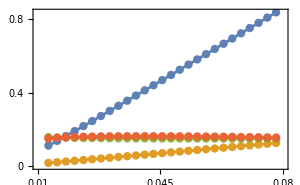

```mathematica
plot21=ListPlot[{pointsSL,pointsV,pointsSF,pointsamp},Joined->True,Mesh->All,PlotRange->{{0.01,0.08},All},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},(*PlotLegends->LineLegend[Automatic,{"Step Length, v","Speed","Step Freq","Amp"}],*)FrameLabel->{{None,None},{MaTeX["\\LARGE \\text{$\\dot{y}_0$}"],None}},ImageSize->{300,200},MeshStyle->PointSize[0.02],FrameTicks->{{tiksfunc[{0,0.4,0.8}],Automatic},{tiksfunc[{0.01,0.045,0.08}],Automatic}}]
```

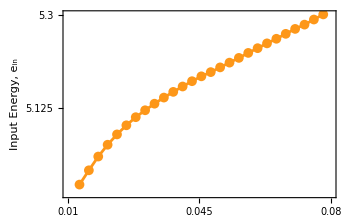

```mathematica
plot211=ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->{{0.01,0.08},All},Frame->True,LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},PlotStyle->ColorData["SunsetColors",0.6],FrameStyle->{{ColorData["SunsetColors",0.6],None},{None,None}},ImageSize->{350,230},MeshStyle->PointSize[0.02],FrameLabel->{{"Input Energy, e_in",None},{MaTeX["\\LARGE \\text{$\\dot{y}_0$}"],None}},FrameTicks->{{tiksfunc[{4.95,5.125,5.3}],Automatic},{tiksfunc[{0.01,0.045,0.08}],Automatic}}]
(*plot212=ListPlot[pointsgrf,Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,17},ImageSize->{350,230},FrameStyle->{{RGBColor[0.2,0.5,0.6],None},{None,None}},PlotStyle->RGBColor[0.2,0.5,0.6],MeshStyle->PointSize[0.02]];
plot22=ResourceFunction["CombinePlots"][plot211,plot212,"AxesSides"->"TwoY",Frame->True,ImageSize->{350,230},FrameLabel->{{"Input Energy, e_in","Abs(GRF)_max"},{MaTeX["\\LARGE \\text{$\\dot{y}(0)$}"],None}},ImagePadding->{{60,80},{60,20}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"}]*)
```

```mathematica
FindFit[pointsSL,a x +b,{a,b},x]
```

{a→11.2218,b→-0.039434}

```mathematica
FindFit[pointsSL,a x +b,{a,b},x]
```

{a→13.0234,b→-0.0502136}

```mathematica
FindFit[pointsV,a x +b,{a,b},x]
```

{a→1.96432,b→-0.00641913}

## Influence of initial height

```mathematica
y0D=Table[i,{i,0.2,1.6,0.1}]
```

{0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6}

```mathematica
results=Table[Module[{ϕ=0.3,γ=0.01,init={0,-0.05,i,0.015,0,0},output,iteration=0,state,ldev=1.5*1,l0=1,δy=-0.05,ke,dke,pe,dpe,totalsynctime,percentCong,zmin,zmax,amp,energyC,grf,grfmin,grfmax},(*Initial state*)

output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@init];

While[Or@@Thread[Abs[output[[3]]]>=10^-4]&&iteration<=1000,
state=output[[1]];
output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@state];
iteration++;];

ke=(0.5*(Sqrt[D[output[[4,2]],t]^2+D[output[[4,3]],t]^2]));
dke=D[ke,t];
pe=(γ(output[[4,3]]));
dpe=D[pe,t];
syncCondition[t]=Piecewise[{{1,dpe*dke>0}},0];
totalsynctime=Quiet@Check[NIntegrate[syncCondition[t],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
percentCong=(totalsynctime/output[[4,4]])*100;

zmin=Quiet@Check[First[FindMinimum[{output[[4,3]],output[[4,1]]<t<output[[1,6]]},{t,(output[[1,6]]+output[[4,1]])/2}]],$Failed];
zmax=output[[4,3]]/.t->output[[4,1]];
amp=(zmax-zmin)/2;
energyC=Quiet@Check[NIntegrate[Abs[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2])(D[(l0-ldev Cos[t-output[[4,1]]]),t])],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
grfmax=Abs[First[Quiet[FindMaximum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[4,1]],output[[1,6]]}]]]];
grfmin=Abs[First[Quiet[FindMinimum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[1,6]],output[[4,1]]}]]]];
grf=Max[grfmin,grfmax];






{output,iteration,{percentCong,amp,energyC,grf}}

],{i,y0D}];
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\z0.mx",results];
```

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\z0.mx"];
```

```mathematica
resultsUU=Table[ReplacePart[results[[i]],1->Delete[results[[i,1]],4]],{i,1,Length[y0D]}];
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
trueresults=Pick[results,truefalse];
trueϕγ=Pick[y0D,truefalse];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
resultsU=filterPoints[resultsUU][[1]];
ϕγU=filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
grf=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
pointsSL=Transpose[{ϕγU,steplength}];
pointsV=Transpose[{ϕγU,speedND}];
pointsSF=Transpose[{ϕγU,stepFreq}];
pointsPC=Transpose[{ϕγU,perCong}];
pointsCon=Transpose[{ϕγU,convergP}];
pointsamp=Transpose[{ϕγU,amp}];
pointsengC=Transpose[{ϕγU,engC}];
pointsgrf=Transpose[{ϕγU,grf}];
```

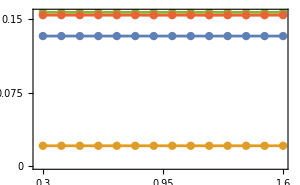

```mathematica
plot31=ListPlot[{pointsSL,pointsV,pointsSF,pointsamp},Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},(*PlotLegends->LineLegend[Automatic,{"Step Length, v","Speed","Step Freq","Amp"}],*)FrameLabel->{{None,None},{MaTeX["\\LARGE \\text{$z_0$}"],None}},ImageSize->{300,200},MeshStyle->PointSize[0.02],FrameTicks->{{tiksfunc[{0,0.075,0.15}],Automatic},{tiksfunc[{0.3,0.95,1.6}],Automatic}}]
```

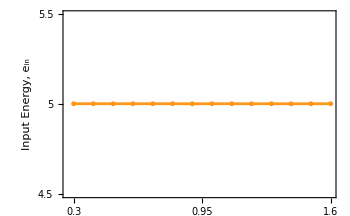

```mathematica
plot311=ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->{Automatic,{4.5,5.5}},Frame->True,PlotStyle->ColorData["SunsetColors",0.6],FrameStyle->{{ColorData["SunsetColors",0.6],None},{None,None}},ImageSize->{350,230},MeshStyle->PointSize[0.01],ImageSize->{300,200},FrameLabel->{{"Input Energy, e_in",None},{MaTeX["\\LARGE \\text{$z_0$}"],None}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},FrameTicks->{{tiksfunc[{4.5,5,5.5}],Automatic},{tiksfunc[{0.3,0.95,1.6}],Automatic}}]
(*plot312=ListPlot[pointsgrf,Joined->True,Mesh->All,PlotRange->{Automatic,{1,2.8}},Frame->True,LabelStyle->{Black,17},ImageSize->{350,230},PlotStyle->RGBColor[0.2,0.5,0.6],FrameStyle->{{RGBColor[0.2,0.5,0.6],None},{None,None}},ImageSize->{350,230},MeshStyle->PointSize[0.02]];
plot32=ResourceFunction["CombinePlots"][plot311,plot312,"AxesSides"->"TwoY",Frame->True,ImageSize->{350,230},FrameLabel->{{"Input Energy, e_in","Abs(GRF)_max"},{MaTeX["\\LARGE \\text{$z(0)$}"],None}},ImagePadding->{{70,70},{60,10}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"}]*)
```

```mathematica
FindFit[pointsengC,a x +b,{a,b},x]
```

{a→-0.000122465,b→5.0027}

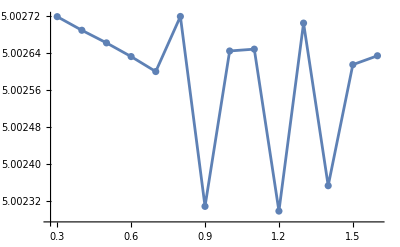

```mathematica
ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->All]
```

## Influence of initial z speed

```mathematica
y0D=Table[i,{i,0,-0.18,-0.01}]
```

{0.,-0.01,-0.02,-0.03,-0.04,-0.05,-0.06,-0.07,-0.08,-0.09,-0.1,-0.11,-0.12,-0.13,-0.14,-0.15,-0.16,-0.17,-0.18}

```mathematica
results=Table[Module[{ϕ=0.3,γ=0.01,init={0,-0.05,1,0.015,i,0},output,iteration=0,state,ldev=1.5*1,l0=1,δy=-0.05,ke,dke,pe,dpe,totalsynctime,percentCong,zmin,zmax,amp,energyC,grf,grfmin,grfmax},(*Initial state*)

output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@init];

While[Or@@Thread[Abs[output[[3]]]>=10^-4]&&iteration<=1000,
state=output[[1]];
output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@state];
iteration++;];

ke=(0.5*(Sqrt[D[output[[4,2]],t]^2+D[output[[4,3]],t]^2]));
dke=D[ke,t];
pe=(γ(output[[4,3]]));
dpe=D[pe,t];
syncCondition[t]=Piecewise[{{1,dpe*dke>0}},0];
totalsynctime=Quiet@Check[NIntegrate[syncCondition[t],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
percentCong=(totalsynctime/output[[4,4]])*100;

zmin=Quiet@Check[First[FindMinimum[{output[[4,3]],output[[4,1]]<t<output[[1,6]]},{t,(output[[1,6]]+output[[4,1]])/2}]],$Failed];
zmax=output[[4,3]]/.t->output[[4,1]];
amp=(zmax-zmin)/2;
energyC=Quiet@Check[NIntegrate[Abs[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2])(D[(l0-ldev Cos[t-output[[4,1]]]),t])],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
grfmax=Abs[First[Quiet[FindMaximum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[4,1]],output[[1,6]]}]]]];
grfmin=Abs[First[Quiet[FindMinimum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[1,6]],output[[4,1]]}]]]];
grf=Max[grfmin,grfmax];





{output,iteration,{percentCong,amp,energyC,grf}}

],{i,y0D}];
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\z0D.mx",results];
```

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\z0D.mx"];
```

```mathematica
resultsUU=Table[ReplacePart[results[[i]],1->Delete[results[[i,1]],4]],{i,1,Length[y0D]}];
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
trueresults=Pick[results,truefalse];
trueϕγ=Pick[y0D,truefalse];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
resultsU=filterPoints[resultsUU][[1]];
ϕγU=filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
grf=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
pointsSL=Transpose[{ϕγU,steplength}];
pointsV=Transpose[{ϕγU,speedND}];
pointsSF=Transpose[{ϕγU,stepFreq}];
pointsPC=Transpose[{ϕγU,perCong}];
pointsCon=Transpose[{ϕγU,convergP}];
pointsamp=Transpose[{ϕγU,amp}];
pointsengC=Transpose[{ϕγU,engC}];
pointsgrf=Transpose[{ϕγU,grf}];
```

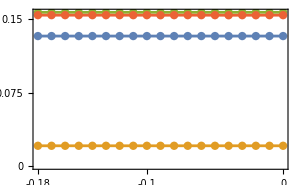

```mathematica
plot41=ListPlot[{pointsSL,pointsV,pointsSF,pointsamp},Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},(*PlotLegends->LineLegend[Automatic,{"Gait Length","Speed","Step Freq","Amp"}],*)FrameLabel->{{None,None},{MaTeX["\\LARGE \\text{$\\dot{z}_0$}"],None}},ImageSize->{300,200},MeshStyle->PointSize[0.02],FrameTicks->{{tiksfunc[{0,0.075,0.15}],Automatic},{tiksfunc[{-0.18,-0.1,0}],Automatic}}]
```

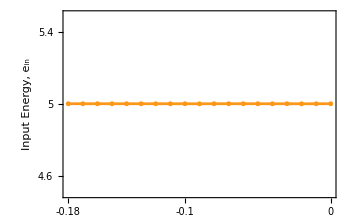

```mathematica
plot411=ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->{Automatic,{4.5,5.5}},Frame->True,PlotStyle->ColorData["SunsetColors",0.6],FrameStyle->{{ColorData["SunsetColors",0.6],None},{None,None}},ImageSize->{350,230},MeshStyle->PointSize[0.01],FrameLabel->{{"Input Energy, e_in",None},{MaTeX["\\LARGE \\text{$\\dot{z}_0$}"],None}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},ImageSize->{350,230},FrameTicks->{{tiksfunc[{4.6,5,5.4}],Automatic},{tiksfunc[{-0.18,-0.1,0}],Automatic}}]
(*plot412=ListPlot[pointsgrf,Joined->True,Mesh->All,PlotRange->{Automatic,{1,2}},Frame->True,LabelStyle->{Black,17},ImageSize->{350,230},FrameStyle->{{RGBColor[0.2,0.5,0.6],None},{None,None}},MeshStyle->PointSize[0.02]];
plot42=ResourceFunction["CombinePlots"][plot411,plot412,"AxesSides"->"TwoY",Frame->True,FrameLabel->{{"Input Energy, e_in","Abs(GRF)_max"},{MaTeX["\\LARGE \\text{$\\dot{z}(0)$}"],None}},ImagePadding->{{70,70},{60,10}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},ImageSize->{350,230}]*)
```

```mathematica
FindFit[pointsgrf,a x +b,{a,b},x]
```

{a→-0.000114287,b→2.78447}

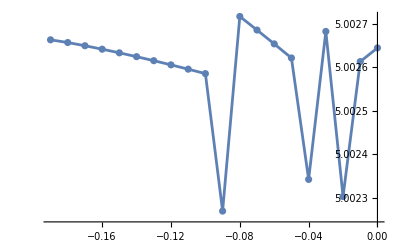

```mathematica
ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->All]
```

## Influence of initial Stepsize

```mathematica
y0D=Table[i,{i,-0.01,-0.06,-0.0025}]
```

{-0.01,-0.0125,-0.015,-0.0175,-0.02,-0.0225,-0.025,-0.0275,-0.03,-0.0325,-0.035,-0.0375,-0.04,-0.0425,-0.045,-0.0475,-0.05,-0.0525,-0.055,-0.0575,-0.06}

```mathematica
results=Table[Module[{ϕ=0.3,γ=0.01,init={0,i,1,0.015,0,0},output,iteration=0,state,ldev=1.5*1,l0=1,δy=i,ke,dke,pe,dpe,totalsynctime,percentCong,zmin,zmax,amp,energyC,grf,grfmin,grfmax},(*Initial state*)

output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@init];

While[Or@@Thread[Abs[output[[3]]]>=10^-4]&&iteration<=1000,
state=output[[1]];
output=functionSolve[ldev,l0,ϕ,γ,δy,Sequence@@state];
iteration++;];

ke=(0.5*(Sqrt[D[output[[4,2]],t]^2+D[output[[4,3]],t]^2]));
dke=D[ke,t];
pe=(γ(output[[4,3]]));
dpe=D[pe,t];
syncCondition[t]=Piecewise[{{1,dpe*dke>0}},0];
totalsynctime=Quiet@Check[NIntegrate[syncCondition[t],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
percentCong=(totalsynctime/output[[4,4]])*100;

zmin=Quiet@Check[First[FindMinimum[{output[[4,3]],output[[4,1]]<t<output[[1,6]]},{t,(output[[1,6]]+output[[4,1]])/2}]],$Failed];
zmax=output[[4,3]]/.t->output[[4,1]];
amp=(zmax-zmin)/2;
energyC=Quiet@Check[NIntegrate[Abs[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2])(D[(l0-ldev Cos[t-output[[4,1]]]),t])],{t,output[[4,1]],output[[1,6]]},PrecisionGoal->3],$Failed];
grfmax=Abs[First[Quiet[FindMaximum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[4,1]],output[[1,6]]}]]]];
grfmin=Abs[First[Quiet[FindMinimum[((l0-ldev Cos[t-output[[4,1]]])-Sqrt[(output[[4,2]]-output[[4,5]])^2+(output[[4,3]])^2]),{t,output[[1,6]],output[[4,1]]}]]]];
grf=Max[grfmin,grfmax];




{output,iteration,{percentCong,amp,energyC,grf}}

],{i,y0D}];
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\δy.mx",results];
```

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Sensitivity\\δy.mx"];
```

```mathematica
resultsUU=Table[ReplacePart[results[[i]],1->Delete[results[[i,1]],4]],{i,1,Length[y0D]}];
filterPoints[results_]:=Module[{truefalse,trueresults,trueϕγ,points},
truefalse=Table[AllTrue[Flatten[results[[i]]],NumericQ],{i,1,Length[results]}];
trueresults=Pick[results,truefalse];
trueϕγ=Pick[y0D,truefalse];
points=Length[trueϕγ];{trueresults,trueϕγ,points}]
resultsU=filterPoints[resultsUU][[1]];
ϕγU=-1filterPoints[resultsUU][[2]];
ϕγUL(*updated length*)=filterPoints[resultsUU][[3]];
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
grf=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
pointsSL=Transpose[{ϕγU,steplength}];
pointsV=Transpose[{ϕγU,speedND}];
pointsSF=Transpose[{ϕγU,stepFreq}];
pointsPC=Transpose[{ϕγU,perCong}];
pointsCon=Transpose[{ϕγU,convergP}];
pointsamp=Transpose[{ϕγU,amp}];
pointsengC=Transpose[{ϕγU,engC}];
pointsgrf=Transpose[{ϕγU,grf}];
```

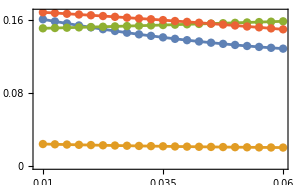

```mathematica
plot61=ListPlot[{pointsSL,pointsV,pointsSF,pointsamp},Joined->True,Mesh->All,PlotRange->All,Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},(*PlotLegends->LineLegend[Automatic,{"Step Length, v","Speed","Step Freq","Amp"}],*)FrameLabel->{{None,None},{MaTeX["\\LARGE \\text{$\\delta{y}$}"],None}},ImageSize->{300,200},MeshStyle->PointSize[0.02],FrameTicks->{{tiksfunc[{0,0.08,0.16}],Automatic},{tiksfunc[{0.06,0.035,0.01}],Automatic}}]
```

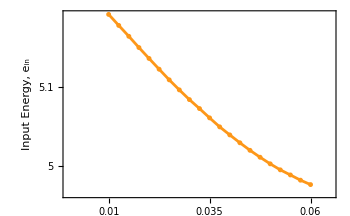

```mathematica
plot611=ListPlot[pointsengC,Joined->True,Mesh->All,PlotRange->{{0.065,0},Automatic},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},PlotStyle->ColorData["SunsetColors",0.6],ImageSize->{350,230},MeshStyle->PointSize[0.01],FrameLabel->{{"Input Energy, e_in",None},{MaTeX["\\LARGE \\text{$\\delta{y}$}"],None}},Frame->True,FrameStyle->{{ColorData["SunsetColors",0.6],None},{None,None}},FrameTicks->{{tiksfunc[{5,5.1,5.2}],Automatic},{tiksfunc[{0.06,0.035,0.01}],Automatic}}]
(*plot612=ListPlot[pointsgrf,Joined->True,Mesh->All,PlotRange->{{0.06,0},Automatic},LabelStyle->{Black,17},ImageSize->{350,230},PlotStyle->RGBColor[0.2,0.5,0.6],MeshStyle->PointSize[0.02]];
plot62=ResourceFunction["CombinePlots"][plot611,plot612,"AxesSides"->"TwoY",Frame->True,ImageSize->{350,230},FrameLabel->{{"Input Energy, e_in","Abs(GRF)_max"},{MaTeX["\\LARGE \\text{$\\delta{y}$}"],None}},ImagePadding->{{80,70},{70,20}},LabelStyle->{Black,17,FontFamily->"Latin Modern Roman 10"},FrameStyle->{{ColorData["SunsetColors",0.6],RGBColor[0.2,0.5,0.6]},{Black,Black}}]*)
```

```mathematica
FindFit[pointsgrf,a x +b,{a,b},x]
```

{a→1.54904,b→2.42235}

```mathematica
FindFit[pointsamp,a x +b,{a,b},x]
```

{a→0.307872,b→0.220418}

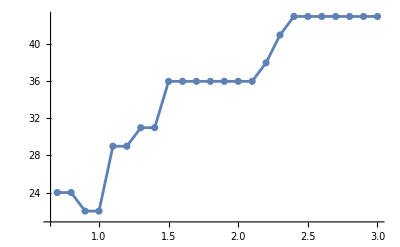

```mathematica
ListPlot[pointsCon,Joined->True,Mesh->All,PlotRange->All]
```

## Combined Plots

```mathematica
dummy=Graphics[ImageSize->{20,20}]
```

-Graphics-

```mathematica
legend=LineLegend[ColorData[97,"ColorList"][[1;;4]],(*First 3 default colors*){"Step Length, Δy","Speed, v","Step Frequency, 1/Δτ","Amplitude, a"} (*Legend labels*),LegendMarkerSize->30,LabelStyle->{16,FontFamily->"Latin Modern Roman 10"}]
```

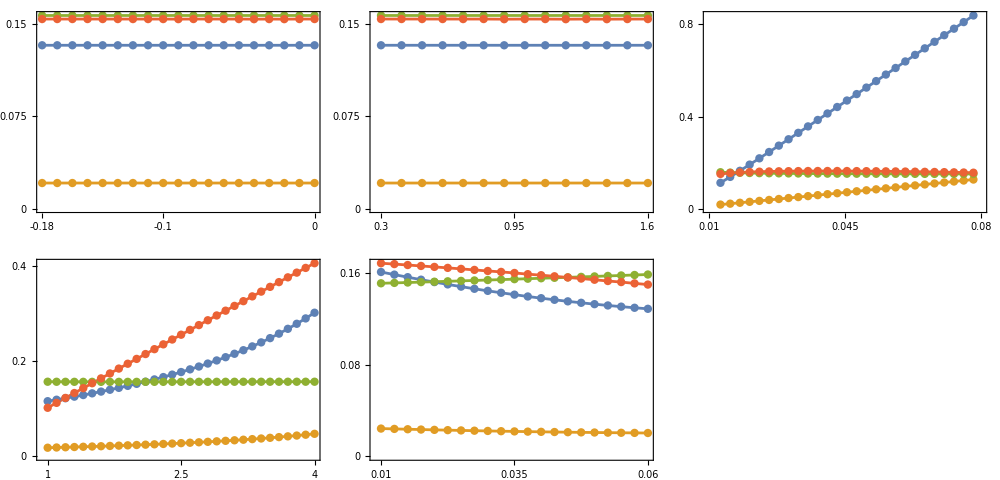

```mathematica
plot=Show[GraphicsGrid[{{plot41,plot31,plot21},{plot11,plot61}},ImageSize->{1000,480},Spacings->{Scaled[0],Scaled[0.1]}],
Graphics[{Text[Style["a",18,FontFamily->"Latin Modern Roman 10"],{35,20}],
Text[Style["b",18,FontFamily->"Latin Modern Roman 10"],{330,20}],
Text[Style["c",18,FontFamily->"Latin Modern Roman 10"],{630,20}],
Text[Style["d",18,FontFamily->"Latin Modern Roman 10"],{35,-200}],
Text[Style["e",18,FontFamily->"Latin Modern Roman 10"],{330,-200}],
Text[Rotate[Style["Non-dimensional Quantity",18,FontFamily->"Latin Modern Roman 10"],Pi/2],{0,-190}]

}]

,Epilog->Inset[legend,(*Your LineLegend object*)Scaled[{1,0.1}]]
]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\GaitCharInfA.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\GaitCharInfA.pdf

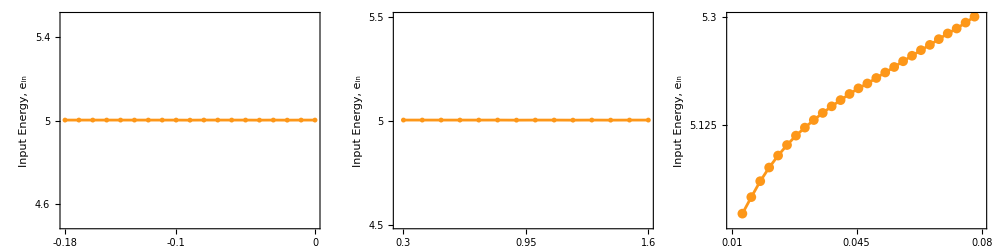

```mathematica
plot1=Show[GraphicsGrid[{{plot411,plot311,plot211}},ImageSize->{1000,250},Spacings->{Scaled[0],Scaled[0]}],
Graphics[{Text[Style["a",18,FontFamily->"Latin Modern Roman 10"],{30,5}]
,Text[Style["b",18,FontFamily->"Latin Modern Roman 10"],{375,5}],
Text[Style["c",18,FontFamily->"Latin Modern Roman 10"],{730,5}]}]
]
```

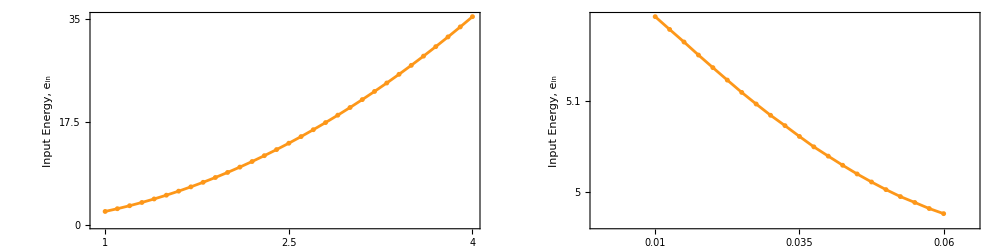

```mathematica
plot2=Show[GraphicsGrid[{{dummy,dummy,plot111,plot611,dummy,dummy}},ImageSize->{1000,250},Spacings->{Scaled[0],Scaled[0]}],
Graphics[{Text[Style["d",18,FontFamily->"Latin Modern Roman 10"],{65,5}]
,Text[Style["e",18,FontFamily->"Latin Modern Roman 10"],{410,5}]
}]
]
```

```mathematica
plot=GraphicsColumn[{plot1,plot2},ImageSize->{960,540},Spacings->{Scaled[0],Scaled[-0.1]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\GaitCharInfB.pdf",plot]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\GaitCharInfB.pdf